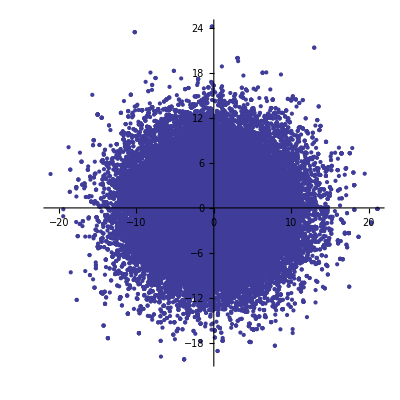

Vel49.4787

```mathematica
dt=Import["/Users/xuhao/Develop/T13/data.out","Table"];
xdt=Table[dt[[i]][[1]]^2,{i,1,Length[dt]}];
ydt=Table[dt[[i]][[2]]^2,{i,1,Length[dt]}];
ndt=Table[Norm[dt[[i]]]^2,{i,1,Length[dt]}];
ListPlot[dt,AspectRatio->1]
Print["Vel",Mean[ndt]]
```

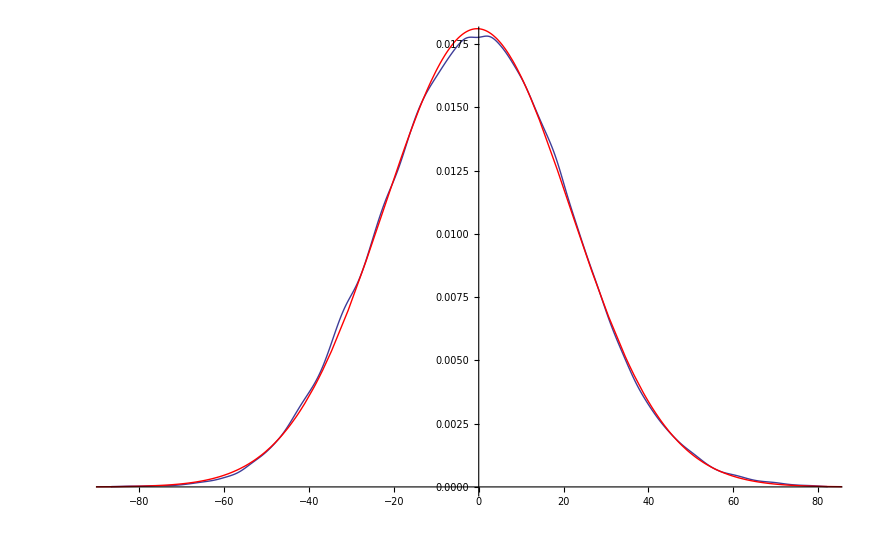

-Graphics-

485.419

494.55

979.969

```mathematica
dtx=Table[dt[[i]][[1]],{i,1,Length[dt]}];
dty=Table[dt[[i]][[1]],{i,1,Length[dt]}];
p01=SmoothHistogram[dtx];p02=Plot[PDF[NormalDistribution[q,w]/.FindDistributionParameters[dtx,NormalDistribution[q,w]]][x],{x,-100,100},PlotStyle->Red];
Show[p01,p02]
p11=SmoothHistogram[dty];p12=Plot[PDF[NormalDistribution[q,w]/.FindDistributionParameters[dty,NormalDistribution[q,w]]][x],{x,-100,100},PlotStyle->Red];
Show[p11,p12]
```

```mathematica
FindDistributionParameters[dtx,NormalDistribution[q,w]]
```

{q→-0.369062,w→22.0291}

```mathematica
Mean[dtx]
```

-0.369062

```mathematica
f[4]
```

```mathematica
f[x_]:=1/2 Erfc[(-0.36906171723958114-x)/(√2 *-0.36906171723958114)];
p[x_]=D[f[x_],x]
```

Rule::rhs: Pattern x_ appears on the right-hand side of rule p[x_].

-1.08096 ⅇ^(-3.6709 (-0.369062-x_)^2) Pattern^(1,0)[x,_]

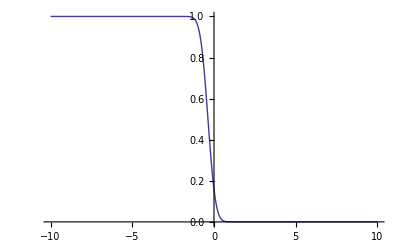

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
f[4]
```

1.23715×10^-32

```mathematica
PDF[NormalDistribution[]]
```

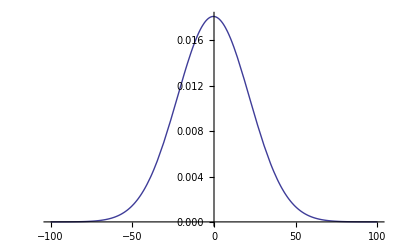

```mathematica
Plot[PDF[NormalDistribution[q,w]/.FindDistributionParameters[dtx,NormalDistribution[q,w]]][x],{x,-100,100}]
```

```mathematica
PDF[NormalDistribution[q,w]/.FindDistributionParameters[dtx,NormalDistribution[q,w]]][100]
```

5.62558×10^-7